```mathematica
Phi=Symbol["Phi"];
Theta=Symbol["Theta"];

Rot={Sin[Phi]*Cos[Theta],Sin[Phi]*Sin[Theta],Cos[Phi]};
(*Rot={Cos[Theta]*Cos[Theta],Cos[Theta]*Sin[Phi],Sin[Phi]};*)

Theta = Pi/2;
Phi=Pi/3;
module = Sqrt[(Sin[Phi]*Cos[Theta])^2 + (Sin[Phi]*Sin[Theta])^2+Cos[Phi]^2]
```

1

```mathematica
Manipulate[Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},1]},Arrow[{{0,0,0},{Sin[Phi]*Cos[Theta],Sin[Phi]*Sin[Theta],Cos[Phi]}}],{Thickness[0.005],Red,Arrow[{{0,0,0},{1.2,0,0}}]},{Thickness[0.005],Green,Arrow[{{0,0,0},{0,1.2,0}}]},{Thickness[0.005],Blue,Arrow[{{0,0,0},{0,0,1.2}}]} },PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True,AxesLabel->{"X","Y","Z"},LabelStyle->Directive[Bold,12],ImageSize->Large],{{Phi,Pi,"Phi"},0,Pi,Pi/100},{{Theta,Pi,"Theta"},0,2 Pi,Pi/100}]
```

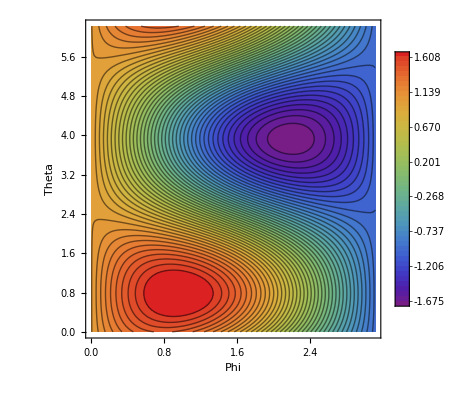

```mathematica
numPoints=100;
phi=Subdivide[0,Pi,numPoints];
theta=Subdivide[0,2 Pi,numPoints];

SingSpinEnergy=Table[S={Sin[phi[[i]]] Cos[theta[[j]]],Sin[phi[[i]]] Sin[theta[[j]]],Cos[phi[[i]]]};
energy=Total[S];
{phi[[i]],theta[[j]],energy},{i,1,numPoints},{j,1,numPoints}];

flatList=Flatten[SingSpinEnergy,1];


ListContourPlot[flatList,Contours->50,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"Phi","Theta"},PlotRange->All]
```

```mathematica
numPoints=100;
phiRange=Subdivide[0,Pi,numPoints];
thetaRange=Subdivide[0,2 Pi,numPoints];

energyList=Flatten[Table[{phi,theta,Sin[phi]+Cos[theta]},(*energy formula*){phi,phiRange},{theta,thetaRange}],1];
Manipulate[Column[{Show[Graphics3D[{{Opacity[0.3],Sphere[]},Arrow[{{0,0,0},{Sin[Phi]*Cos[Theta],Sin[Phi]*Sin[Theta],Cos[Phi]}}],{Dashed,Red,Line[{{-1.5,0,0},{1.5,0,0}}]},{Dashed,Green,Line[{{0,-1.5,0},{0,1.5,0}}]},{Dashed,Blue,Line[{{0,0,-1.5},{0,0,1.5}}]} },PlotRange->1.5,ImageSize->Medium],ViewPoint->{1.3,-2.4,2.0}],ListContourPlot[energyList,Contours->50,ColorFunction->"Rainbow",FrameLabel->{"Phi","Theta"},PlotLegends->Automatic,PlotRange->All,Epilog->{PointSize[0.02],Point[{Phi,Theta}]} ]}],{{Phi,Pi/2,"Phi"},0,Pi,Pi/100},{{Theta,Pi,"Theta"},0,2 Pi,Pi/100}]
```

```mathematica
Manipulate[Row[{Show[Graphics3D[{{Opacity[0.3],Sphere[]},Arrow[{{0,0,0},{Sin[Phi]*Cos[Theta],Sin[Phi]*Sin[Theta],Cos[Phi]}}],{Dashed,Red,Line[{{-1.5,0,0},{1.5,0,0}}]},{Dashed,Green,Line[{{0,-1.5,0},{0,1.5,0}}]},{Dashed,Blue,Line[{{0,0,-1.5},{0,0,1.5}}]}},PlotRange->1.5,ImageSize->Medium],ViewPoint->{1.3,-2.4,2.0}],ListContourPlot[flatList,Contours->50,ColorFunction->"Rainbow",FrameLabel->{"Phi","Theta"},PlotLegends->Automatic,PlotRange->All,Epilog->{PointSize[0.02],Point[{Phi,Theta}]},ImageSize->Medium]}],{{Phi,Pi/2,"Phi"},0,Pi,Pi/10},{{Theta,Pi,"Theta"},0,2 Pi,Pi/10}]
```